# CRMSD and D

## data loading

```mathematica
p0s={3.9,3.85,3.825,3.80,3.775,3.75};
```

```mathematica
temperatures={{0.039,0.01,0.005,0.002,0.001,0.0005,0.00033,0.00014,0.000091,0.000077,0.000054,0.000045,0.000036},{0.039 ,0.016, 0.01 ,0.005 ,0.00385, 0.0025 ,0.002, 0.001 ,0.0005 ,0.00033 ,0.00025, 0.00014, 0.000091,0.000077,0.000054, 0.000045, 0.000036},{0.063 ,0.039, 0.03105, 0.016 ,0.01, 0.008, 0.0063, 0.005 ,0.00385, 0.0031, 0.0025, 0.002, 0.0015, 0.001, 0.00067 ,0.0005},{0.063 ,0.039 ,0.03105, 0.025, 0.016 ,0.01 ,0.008 ,0.0063, 0.005, 0.00385, 0.0031, 0.0028 ,0.0025 ,0.0022},{0.03105, 0.025 ,0.02 ,0.016 ,0.012, 0.01, 0.009 ,0.008 ,0.0075, 0.007 ,0.0063, 0.0056 ,0.0054},{0.063, 0.039, 0.03105, 0.025 ,0.02, 0.016, 0.014,0.012 ,0.011, 0.01, 0.0093}};
 records={{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19}};
tauEstimate={{0.596396,1.36006,8.39117,8.32344,46.2416,35.0693,135.321,564.239,829.48,897.484,1365.27,1522.57,3000},{2, 4,10, 20, 40,60, 80, 200, 500, 800, 999999, 999999, 999999,999999, 999999, 999999, 999999},{1, 2, 4 ,9 ,15,25, 40 ,60, 80, 120,200 ,300 ,1000 ,999999, 999999,999999},{1, 3, 4 ,8 ,15,40 ,70 ,150 ,250, 600 ,2000, 999999 ,999999, 999999},{2, 10,20 ,30, 80 ,100 ,400 ,500 ,2500 ,2500, 3000 ,7000, 10000},{4 ,5 ,7 ,10 ,30 ,70, 150 ,700,1400, 4000 ,9500}};
```

```mathematica
NumberForm[Floor[1522.57*10],{8,0}]
```

15225

```mathematica
CRTrueMSDs=Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p","/timeTrueCRMSD_N4096_p","_T","_waitingTime","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],Floor[If[tauEstimate[[p,T]]==999999,tauEstimate[[p,T]],If[tauEstimate[[p,T]]<1000,10000,tauEstimate[[p,T]]*10]]],records[[p,i]]},{3,4,8,0,0}],"Data"],{i,Length[records[[p]]]}],$Failed|_Missing|_Part],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.900/timeTrueCRMSD_N4096_p3.9000_T0.03900000_waitingTime10000_idx17.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.900/timeTrueCRMSD_N4096_p3.9000_T0.03900000_waitingTime10000_idx19.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.900/timeTrueCRMSD_N4096_p3.9000_T0.01000000_waitingTime10000_idx18.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

```mathematica
trueMSDs=Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p","/timeTrueMSD_N4096_p","_T","_waitingTime","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],Floor[If[tauEstimate[[p,T]]==999999,tauEstimate[[p,T]],If[tauEstimate[[p,T]]<1000,10000,tauEstimate[[p,T]]*10]]],records[[p,i]]},{3,4,8,0,0}],"Data"],{i,Length[records[[p]]]}],$Failed],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.900/timeTrueMSD_N4096_p3.9000_T0.01000000_waitingTime10000_idx18.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.900/timeTrueMSD_N4096_p3.9000_T0.03900000_waitingTime10000_idx19.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.900/timeTrueMSD_N4096_p3.9000_T0.03900000_waitingTime10000_idx17.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.900/timeTrueMSD_N4096_p3.9000_T0.01000000_waitingTime10000_idx18.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.900/timeTrueMSD_N4096_p3.9000_T0.03900000_waitingTime10000_idx19.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.900/timeTrueMSD_N4096_p3.9000_T0.03900000_waitingTime10000_idx17.nc not found during Import.

```mathematica
time=Table[Table[Table[Mean[DeleteCases[Table[CRTrueMSDs[[p,T,i,1,rec]],{i,Length[CRTrueMSDs[[p,T]]]}],_Missing|_Part]],{rec,Max[Table[Length[CRTrueMSDs[[p,T,i,1]]],{i,Length[CRTrueMSDs[[p,T]]]}]]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 640 of … does not exist.

Part::partw: Part 113 of … does not exist.

Part::partw: Part 114 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
CRTrueMSDMean=Table[Table[Table[Mean[DeleteCases[Table[CRTrueMSDs[[p,T,i,2,rec]],{i,Length[CRTrueMSDs[[p,T]]]}],_Missing|_Part]],{rec,Max[Table[Length[CRTrueMSDs[[p,T,i,1]]],{i,Length[CRTrueMSDs[[p,T]]]}]]-1}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 113 of … does not exist.

Part::partw: Part 114 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
Normal[CRTrueMSDs[[1,14,1,1]]]-CRTrueMSDs[[1,14,1,1,1]]
```

```mathematica
trueMSDMean=Table[Table[Table[Mean[DeleteCases[Table[trueMSDs[[p,T,i,2,rec]],{i,Length[trueMSDs[[p,T]]]}],_Missing|_Part]],{rec,Max[Table[Length[trueMSDs[[p,T,i,1]]],{i,Length[trueMSDs[[p,T]]]}]]-1}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 113 of … does not exist.

Part::partw: Part 114 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

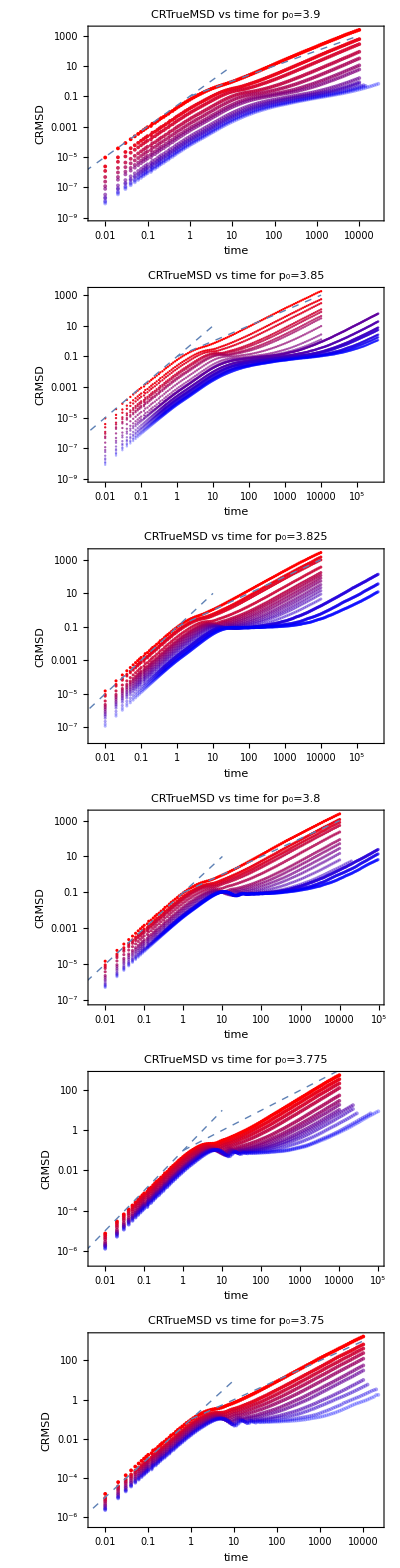

```mathematica
CRMSDTrueMeanPlots=Table[Show[
ListLogLogPlot[Table[Table[{time[[p,T,rec+1]]-time[[p,T,1]],CRTrueMSDMean[[p,T,rec]]},{rec,Length[CRTrueMSDMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","CRMSD"},ImageSize->600,PlotLabel->"CRTrueMSD vs time for p_0="<>ToString[p0s[[p]]],Joined->False],LogLogPlot[.1x,{x,1,10000},PlotStyle->{Dashed,Thick}],LogLogPlot[.1x^2,{x,0.001,10},PlotStyle->{Dashed,Thick}]],{p,Length[p0s]}];
Column[CRMSDTrueMeanPlots]
```

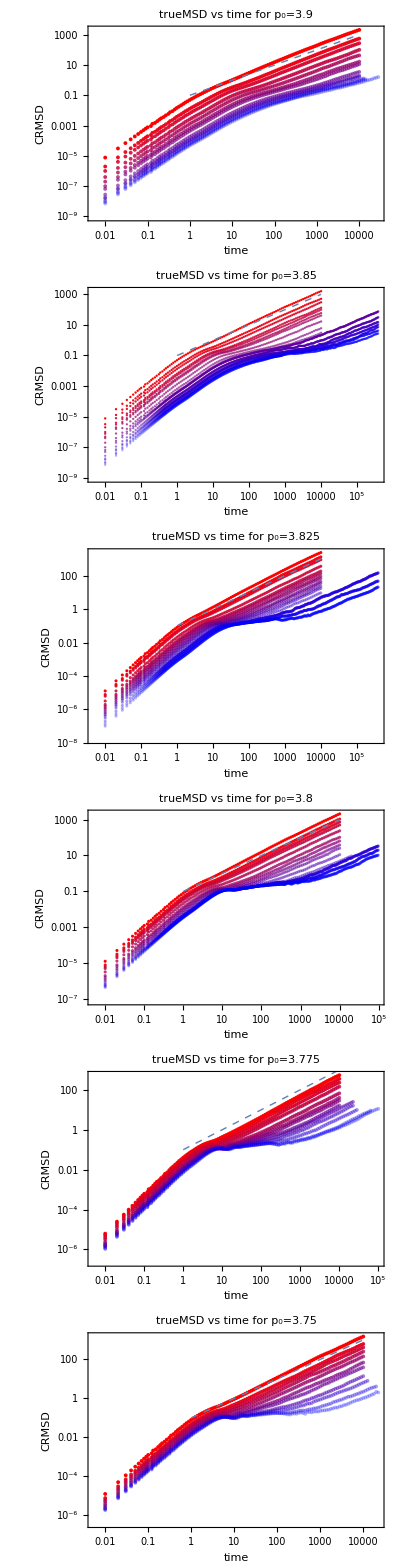

```mathematica
trueMSDMeanPlots=Table[Show[
ListLogLogPlot[Table[Table[{time[[p,T,rec+1]]-time[[p,T,1]],trueMSDMean[[p,T,rec]]},{rec,Length[trueMSDMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","CRMSD"},ImageSize->600,PlotLabel->"trueMSD vs time for p_0="<>ToString[p0s[[p]]],Joined->False],LogLogPlot[.1x,{x,1,10000},PlotStyle->{Dashed,Thick}]],{p,Length[p0s]}];
Column[trueMSDMeanPlots]
```

### Diffusion constant defined as lim_(t->inf) MSD/t

```mathematica
diffusion=Table[Table[trueMSDMean[[p,T,Length[trueMSDMean[[p,T]]]]]/(time[[p,T,Length[trueMSDMean[[p,T]]]+1]]-time[[p,T,1]]),{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{0.209242,0.055354,0.0274041,0.0101511,0.00431389,0.00168148,0.00113189,0.000351088,0.000200741,0.000168423,0.000102771,0.000080954,0.0000572416},{0.159315,0.0507787,0.030056,0.0133152,0.00987184,0.0058798,0.0040367,0.0016734,0.000604835,0.000307695,0.000195214,0.0000815757,0.0000384783,0.0000274625,0.0000188878,0.0000111734,7.15206×10^-6},{0.239791,0.13202,0.0896004,0.0363334,0.0186791,0.0134194,0.00911439,0.00673546,0.00451451,0.00349349,0.00236,0.00172015,0.000926428,0.00036649,0.000119177,0.000051277},{0.208301,0.106793,0.0731399,0.050006,0.0237055,0.0103774,0.00643379,0.00383899,0.00252275,0.00111001,0.000464777,0.000344724,0.000205638,0.000107405},{0.0539391,0.0353622,0.0231274,0.0144337,0.00667272,0.0039783,0.00288137,0.0016496,0.00110692,0.000719537,0.000348023,0.000144715,0.000112226},{0.148696,0.0618204,0.0411178,0.0251799,0.0141926,0.00690251,0.00393376,0.00138325,0.000634746,0.000205173,0.0000898753}}

```mathematica
diffusion1=Table[Table[trueMSDMean[[p,T,Length[trueMSDMean[[p,T]]]-1]]/(time[[p,T,Length[trueMSDMean[[p,T]]]-1+1]]-time[[p,T,1]]),{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{0.161685,0.050469,0.0300047,0.013156,0.00966075,0.00595904,0.00409995,0.00169851,0.000592138,0.000298393,0.000194868,0.0000820285,0.0000389785,0.000026392,0.0000186656,0.0000108011,7.12412×10^-6},{0.241857,0.132715,0.0893904,0.0365123,0.0188742,0.0132094,0.00919105,0.00668337,0.00446624,0.00344824,0.00237759,0.00174522,0.000946641,0.000368108,0.000119897,0.0000531508},{0.210237,0.109115,0.0732902,0.0498458,0.0236333,0.0104173,0.00638306,0.00381536,0.0025765,0.00107443,0.000468191,0.000348295,0.000204508,0.000108805},{0.0544671,0.0352644,0.0237985,0.014382,0.00672053,0.00390662,0.00282667,0.00167418,0.00112972,0.000747856,0.000349805,0.000141758,0.000116326},{0.148704,0.0623288,0.0408953,0.0245185,0.0141019,0.00707867,0.00396882,0.00137677,0.000636302,0.000210679,0.000107411}}

```mathematica
diffusion5=Table[Table[trueMSDMean[[p,T,Length[trueMSDMean[[p,T]]]-5]]/(time[[p,T,Length[trueMSDMean[[p,T]]]-5+1]]-time[[p,T,1]]),{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{0.157881,0.0523623,0.0290555,0.0129067,0.00958256,0.00621364,0.00405707,0.00177297,0.000612317,0.000305625,0.000189062,0.0000804755,0.0000402963,0.0000255421,0.0000190985,0.0000108363,7.32057×10^-6},{0.245874,0.126313,0.08961,0.0364379,0.0187991,0.0134557,0.00907451,0.00690022,0.00451277,0.0034105,0.00240998,0.00169181,0.000936413,0.000366492,0.000120768,0.0000527337},{0.206367,0.107328,0.0720288,0.0486578,0.0246102,0.0111978,0.00659275,0.00394931,0.00247739,0.00110674,0.000479607,0.000355196,0.000205935,0.000110367},{0.055522,0.0353887,0.0239242,0.0142074,0.00674949,0.00387563,0.00283164,0.00162336,0.00114353,0.000712211,0.000353502,0.000145652,0.000121509},{0.148201,0.0606641,0.0410743,0.0238375,0.0137878,0.00647971,0.00401832,0.00137514,0.000635631,0.000221036,0.000099341}}

```mathematica
CRdiffusion=Table[Table[CRTrueMSDMean[[p,T,Length[CRTrueMSDMean[[p,T]]]]]/(time[[p,T,Length[CRTrueMSDMean[[p,T]]]+1]]-time[[p,T,1]]),{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{0.237363,0.0582227,0.0270308,0.00853989,0.00310112,0.00108837,0.000581886,0.000156683,0.0000848035,0.0000677679,0.0000422334,0.0000337864,0.0000233994},{0.18032,0.0539819,0.029689,0.0117144,0.00796401,0.00430161,0.0030576,0.000950052,0.000268155,0.000127126,0.000161245,0.0000494808,0.0000197356,0.000013926,6.79956×10^-6,4.55961×10^-6,3.02121×10^-6},{0.273571,0.147253,0.099705,0.0369247,0.0173888,0.0117968,0.00808002,0.00540136,0.00332991,0.00219315,0.00143458,0.000898324,0.000457685,0.000350697,0.0000945611,0.0000315917},{0.235815,0.114716,0.0789733,0.0530962,0.0229792,0.00870578,0.00515962,0.0028168,0.0014765,0.000640345,0.00028016,0.000252401,0.000143003,0.0000695441},{0.0562536,0.0356011,0.0219328,0.012891,0.0055078,0.0029687,0.001878,0.00105874,0.000805275,0.000518482,0.000249693,0.000112026,0.0000890381},{0.167574,0.0658728,0.0407487,0.0238225,0.0123429,0.00556242,0.00306303,0.00100638,0.000461675,0.000165857,0.0000777463}}

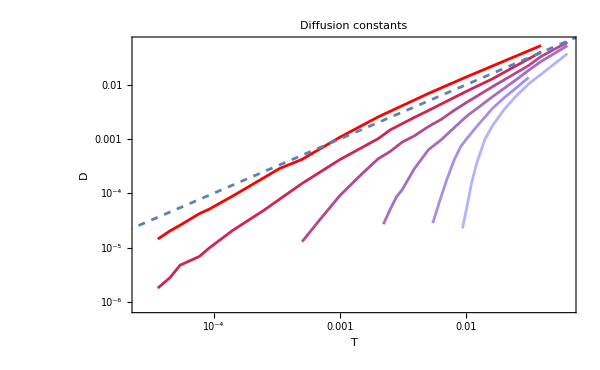

```mathematica
diffusionConstPlots=Show[ListLogLogPlot[Table[Table[{temperatures[[p,T]],diffusion[[p,T]]/4},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}],Joined->True,PlotStyle->redBluePlotConfig[Length[p0s]],FrameLabel->{"T","D"},ImageSize->600,PlotLabel->"Diffusion constants"],LogLogPlot[x,{x,0.00001,0.1},PlotStyle->Dashed]]
```

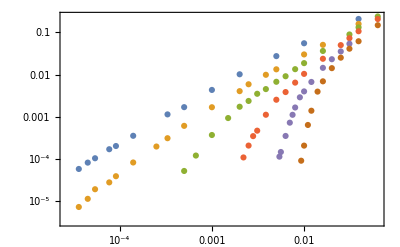

```mathematica
ListLogLogPlot[Table[Table[{temperatures[[p,T]],diffusion[[p,T]]},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]]
```

```mathematica
(*MSD in Daniel's paper*)
MSDpaper={{0.02744749241872213,0.0007787583475777915},
{0.0514315895080298,0.0014551103426274877},
{0.1000000000000001,0.0026078919439150756},
{0.23387508439166665,0.005080218046913028},
{0.40702929570271873,0.0080348426383541},
{0.7626985859023452,0.012707859313704488},
{1.538741884408703,0.020098674685430508},
{2.7787550653702198,0.028051998106045035},
{5.606129189998862,0.03915256155232898},
{9.756741816936332,0.048223410150691405},
{19.684194472866192,0.05939578904572267},
{28.480358684358105,0.06730608019616548},
{66.60846290809181,0.09010546478929268},
{120.2856733658804,0.115704011481292},
{187.38174228603867,0.1425102670302998},
{291.904400246814,0.18299677618038562},
{438.2392079060478,0.23498531572671966},
{634.0726742929744,0.30174355942071884},
{917.4171298046817,0.40395672411076433},
{1377.3281798599119,0.5407937629806314},
{2067.797573651249,0.7869145977415526},
{2991.8225338310194,1.053475486498788},
{4328.761281083071,1.470350299935503},
{6263.130254791473,2.052188239999369},
{9402.904648067826,2.9861603330415765},
{13111.339374215684,4.167825258028193},
{18970.329150362097,5.817091329374349},
{29552.092352028998,8.82472859400099},
{59621.24896322193,17.922296801258483}};
```

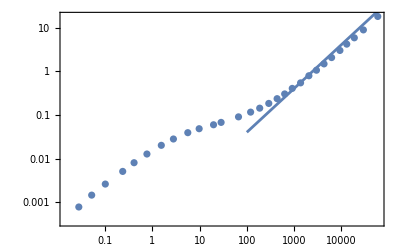

```mathematica
Show[ListLogLogPlot[Table[{MSDpaper[[i,1]],MSDpaper[[i,2]]},{i,Length[MSDpaper]}]],LogLogPlot[0.0004x,{x,100,100000}]]
```

### Fit to MSD~At^1

```mathematica
powerLaw[x_,A_,B_]:=4 A x^B;
```

```mathematica
fittingOffsetfromEnd={{15,15,15,10,10,10,10,8,5,5,5,5,5,5,5,5,5,5},{15,15,15,10,10,10,10,8,5,5,20,20,20,20,20,20,20,20},{15,15,15,15,15,15,10,10,10,10,8,8,8,20,20,20},{15,15,15,15,15,10,10,10,10,10,5,20,20,20,20,20},{15,15,15,15,10,10,10,10,15,15,15,8,8},{15,15,15,15,15,15,5,5,5,5,5}};
```

```mathematica
Table[Table[Table[{time[[p,T,rec+1]]-time[[p,T,Length[trueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]+1]],CRTrueMSDMean[[p,T,rec]]-CRTrueMSDMean[[p,T,Length[trueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]]]},{rec,Length[trueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]],Length[trueMSDMean[[p,T]]]}],{T,1}],{p,1}]
```

{{{{0.,0.},{153.61,28.1636},{325.96,61.2328},{519.35,98.5884},{736.33,141.672},{979.79,187.156},{1252.96,242.819},{1559.45,306.836},{1903.35,375.353},{2289.2,450.949},{2722.14,539.039},{3207.91,645.851},{3752.94,771.912},{4364.48,914.466},{5050.64,1074.1},{5820.53,1244.29}}}}

```mathematica
fitsCRTrueMSD=Table[Table[NonlinearModelFit[Table[{time[[p,T,rec+1]]-time[[p,T,Length[trueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]]],CRTrueMSDMean[[p,T,rec]]-CRTrueMSDMean[[p,T,Length[trueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]-1]]},{rec,Length[trueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]+1,Length[trueMSDMean[[p,T]]]}],{powerLaw[t,A,1]},{A},t,MaxIterations->1000000],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}}

```mathematica
fitsTrueMSD=Table[Table[NonlinearModelFit[Table[{time[[p,T,rec+1]]-time[[p,T,Length[trueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]]],trueMSDMean[[p,T,rec]]-trueMSDMean[[p,T,Length[trueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]-1]]},{rec,Length[trueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]+1,Length[trueMSDMean[[p,T]]]}],{powerLaw[t,A,1]},{A},t,MaxIterations->1000000],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}}

```mathematica
ToString[t^2]
```

2
t

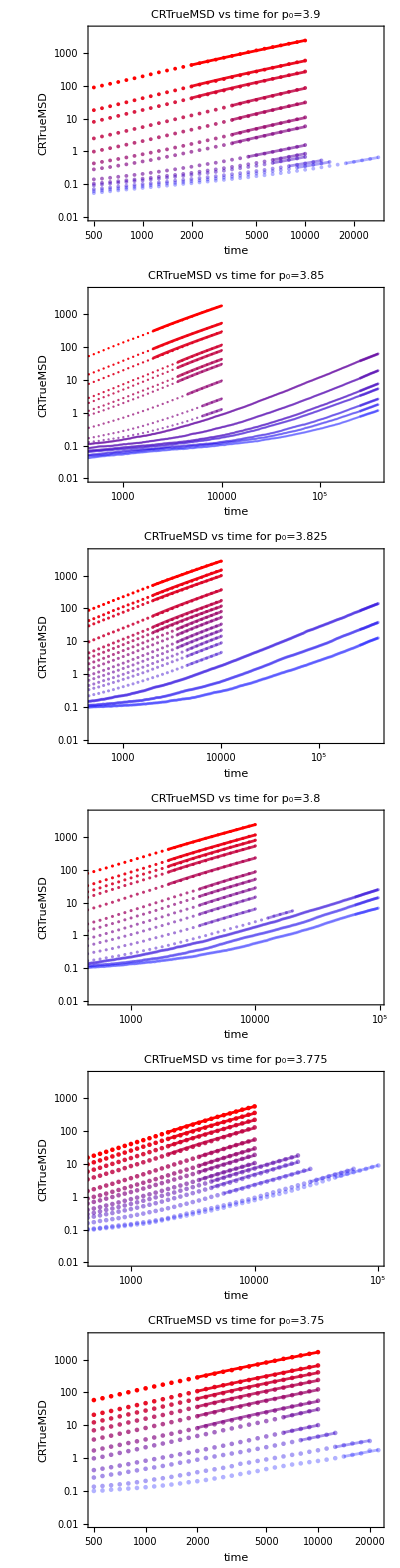

```mathematica
CRTrueMSDMeanPlotsWithFits=Table[Show[
ListLogLogPlot[Table[Table[{time[[p,T,rec+1]]-time[[p,T,1]],CRTrueMSDMean[[p,T,rec]]},{rec,Length[CRTrueMSDMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","CRTrueMSD"},ImageSize->600,PlotLabel->"CRTrueMSD vs time for p_0="<>ToString[p0s[[p]]],Joined->False,PlotRange->{{500,All},{0.01,5000}},ImageSize->600],ListLogLogPlot[Table[Table[{time[[p,T,t+1]]-time[[p,T,1]],fitsCRTrueMSD[[p,T]][time[[p,T,t+1]]-time[[p,T,Length[trueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]+1]]]+CRTrueMSDMean[[p,T,Length[trueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]]]},{t,Length[CRTrueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]+1,Length[CRTrueMSDMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],Joined->True]],{p,Length[p0s]}];
Column[CRTrueMSDMeanPlotsWithFits]
```

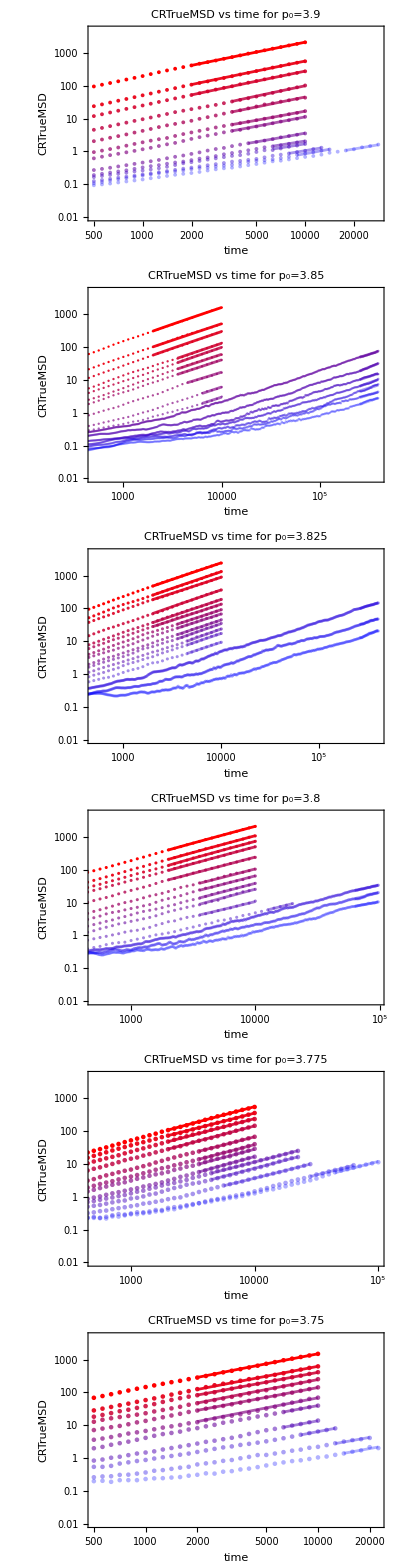

```mathematica
trueMSDMeanPlotsWithFits=Table[Show[
ListLogLogPlot[Table[Table[{time[[p,T,rec+1]]-time[[p,T,1]],trueMSDMean[[p,T,rec]]},{rec,Length[CRTrueMSDMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","CRTrueMSD"},ImageSize->600,PlotLabel->"CRTrueMSD vs time for p_0="<>ToString[p0s[[p]]],Joined->False,PlotRange->{{500,All},{0.01,5000}},ImageSize->600],ListLogLogPlot[Table[Table[{time[[p,T,t+1]]-time[[p,T,1]],fitsTrueMSD[[p,T]][time[[p,T,t+1]]-time[[p,T,Length[trueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]+1]]]+trueMSDMean[[p,T,Length[trueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]]]},{t,Length[CRTrueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]+1,Length[CRTrueMSDMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],Joined->True]],{p,Length[p0s]}];
Column[trueMSDMeanPlotsWithFits]
```

```mathematica
diffusionDirectLinearFit=Table[Table[4*fitsTrueMSD[[p,T]]["BestFitParameters"][[1,2]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{0.21182,0.056649,0.0281073,0.01023,0.00454602,0.00158732,0.00108543,0.000330379,0.0001699,0.000140518,0.0000880267,0.0000756948,0.0000494922},{0.162288,0.0515601,0.0300399,0.0131374,0.0100113,0.00600914,0.0040504,0.00162507,0.000602505,0.000289622,0.000179518,0.0000941144,0.0000409047,0.0000273503,0.0000171679,0.0000102805,7.39664×10^-6},{0.245061,0.132174,0.0880773,0.0369907,0.0187933,0.013328,0.00903634,0.00667462,0.00442649,0.00347,0.00247268,0.00174289,0.000928889,0.000343168,0.000124562,0.0000624381},{0.211562,0.109594,0.0743454,0.0503822,0.024099,0.0103566,0.00638595,0.00382428,0.00257978,0.00100917,0.000445328,0.000291629,0.000191071,0.0000771522},{0.0554271,0.0348446,0.0237837,0.0143317,0.00655354,0.00382573,0.00278327,0.00169557,0.00111627,0.000724501,0.000340559,0.000140003,0.000116476},{0.150636,0.0622011,0.0404599,0.0247248,0.013977,0.00689116,0.0038733,0.00134349,0.000644259,0.000204161,0.0000940916}}

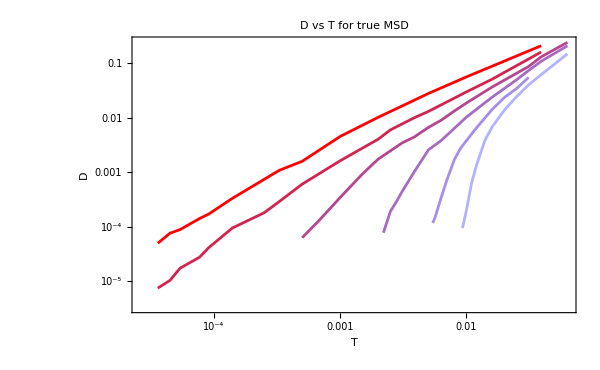

```mathematica
diffusionConstPlots=ListLogLogPlot[Table[Table[{temperatures[[p,T]],4*fitsTrueMSD[[p,T]]["BestFitParameters"][[1,2]]},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}],PlotStyle->redBluePlotConfig[Length[p0s]],FrameLabel->{"T","D"},PlotLabel->"D vs T for true MSD",Joined->True,ImageSize->600]
```

Part::partw: Part 2 of {A→0.040572} does not exist.

Part::partw: Part 2 of {A→0.01289} does not exist.

Part::partw: Part 2 of {A→0.00750997} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

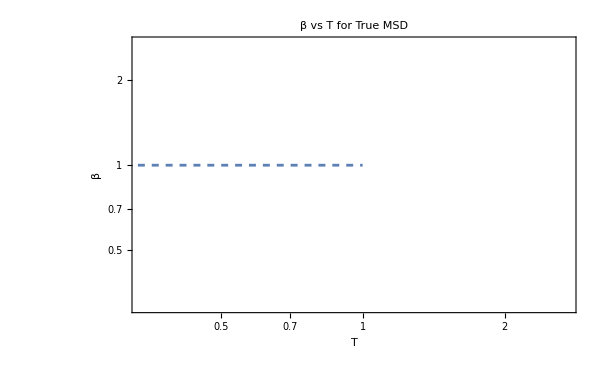

```mathematica
exponenPlots=Show[ListLogLogPlot[Table[Table[{temperatures[[p,T]],fitsTrueMSD[[p,T]]["BestFitParameters"][[2,2]]},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}],PlotStyle->redBluePlotConfig[Length[p0s]],FrameLabel->{"T","β"},PlotLabel->"β vs T for True MSD",Joined->True,ImageSize->600],LogLogPlot[1,{x,0.00001,1},PlotStyle->Dashed]]
```

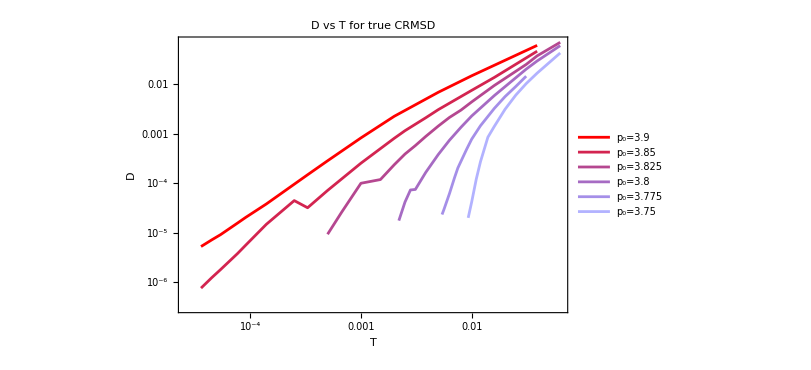

```mathematica
CRdiffusionConstPlots=ListLogLogPlot[Table[Table[{temperatures[[p,T]],fitsCRTrueMSD[[p,T]]["BestFitParameters"][[1,2]]},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}],PlotStyle->redBluePlotConfig[Length[p0s]],FrameLabel->{"T","D"},PlotLabel->"D vs T for true CRMSD",Joined->True,PlotLegends->Table["p_0="<>ToString[p0s[[p]]],{p,Length[p0s]}],ImageSize->600]
```

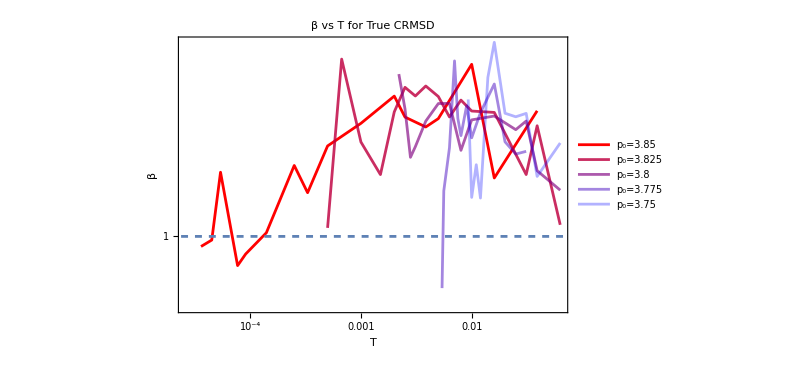

```mathematica
CRexponenPlots=Show[ListLogLogPlot[Table[Table[{temperatures[[p,T]],fitsCRTrueMSD[[p,T]]["BestFitParameters"][[2,2]]},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}],PlotStyle->redBluePlotConfig[Length[p0s]],FrameLabel->{"T","β"},PlotLabel->"β vs T for True CRMSD",PlotLegends->Table["p_0="<>ToString[p0s[[p]]],{p,Length[p0s]}],Joined->True,ImageSize->600],LogLogPlot[1,{x,0.00001,1},PlotStyle->Dashed]]
```

```mathematica
Export["/home/chengling/Research/updates/05232024/MSDfittingNew.jpeg",Grid[Partition[{diffusionConstPlots,CRdiffusionConstPlots,exponenPlots,CRexponenPlots},2]],ImageResolution->800]
```

/home/chengling/Research/updates/05232024/MSDfittingNew.jpeg

```mathematica
Export["/home/chengling/Research/updates/05232024/MSDNew.jpeg",Grid[Partition[{trueMSDMeanPlotsWithFits[[1]],CRTrueMSDMeanPlotsWithFits[[1]],trueMSDMeanPlotsWithFits[[2]],CRTrueMSDMeanPlotsWithFits[[2]],trueMSDMeanPlotsWithFits[[3]],CRTrueMSDMeanPlotsWithFits[[3]]},2]],ImageResolution->800]
```

/home/chengling/Research/updates/05232024/MSDNew.jpeg

### fit it to linear model

```mathematica
LinearFitsCRTrueMSD=Table[Table[LinearModelFit[Table[{time[[p,T,rec+1]]-time[[p,T,Length[trueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]+1]],CRTrueMSDMean[[p,T,rec]]-CRTrueMSDMean[[p,T,Length[trueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]]]},{rec,Length[trueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]+1,Length[trueMSDMean[[p,T]]]}],t,t,IncludeConstantBasis->False],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}}

```mathematica
LinearFitsTrueMSD=Table[Table[LinearModelFit[Table[{time[[p,T,rec+1]]-time[[p,T,Length[trueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]+1]],trueMSDMean[[p,T,rec]]-trueMSDMean[[p,T,Length[trueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]]]},{rec,Length[trueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]+1,Length[trueMSDMean[[p,T]]]}],t,t,IncludeConstantBasis->False],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}}

```mathematica
ToString[t^2]
```

2
t

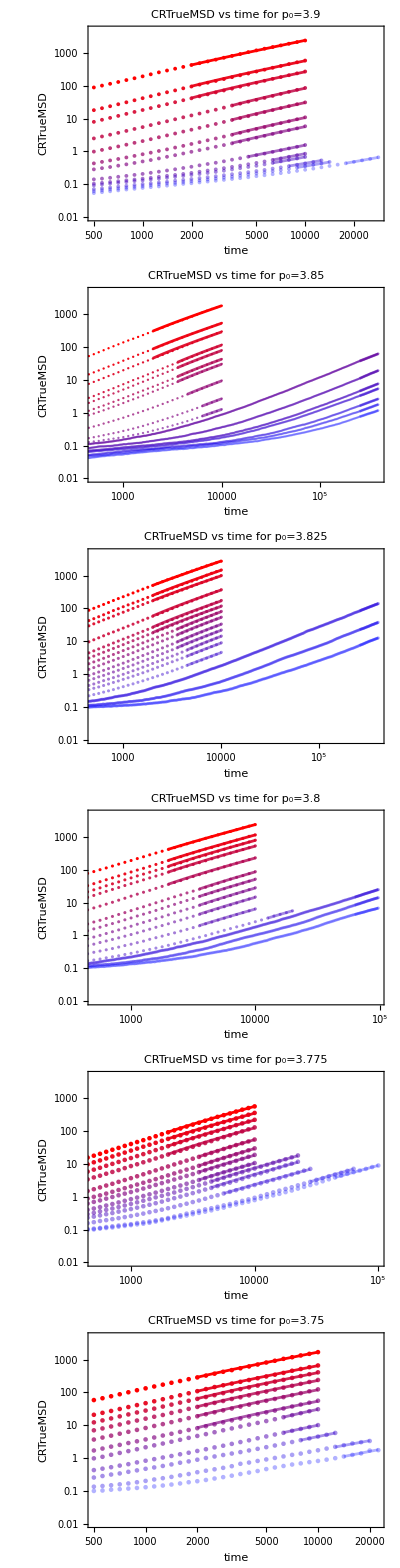

```mathematica
CRTrueMSDMeanPlotsWithLinearFits=Table[Show[
ListLogLogPlot[Table[Table[{time[[p,T,rec+1]]-time[[p,T,1]],CRTrueMSDMean[[p,T,rec]]},{rec,Length[CRTrueMSDMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","CRTrueMSD"},ImageSize->600,PlotLabel->"CRTrueMSD vs time for p_0="<>ToString[p0s[[p]]],Joined->False,PlotRange->{{500,All},{0.01,5000}},ImageSize->600],ListLogLogPlot[Table[Table[{time[[p,T,t+1]]-time[[p,T,1]],LinearFitsCRTrueMSD[[p,T]][time[[p,T,t+1]]-time[[p,T,Length[trueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]+1]]]+CRTrueMSDMean[[p,T,Length[trueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]]]},{t,Length[CRTrueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]+1,Length[CRTrueMSDMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],Joined->True]],{p,Length[p0s]}];
Column[CRTrueMSDMeanPlotsWithLinearFits]
```

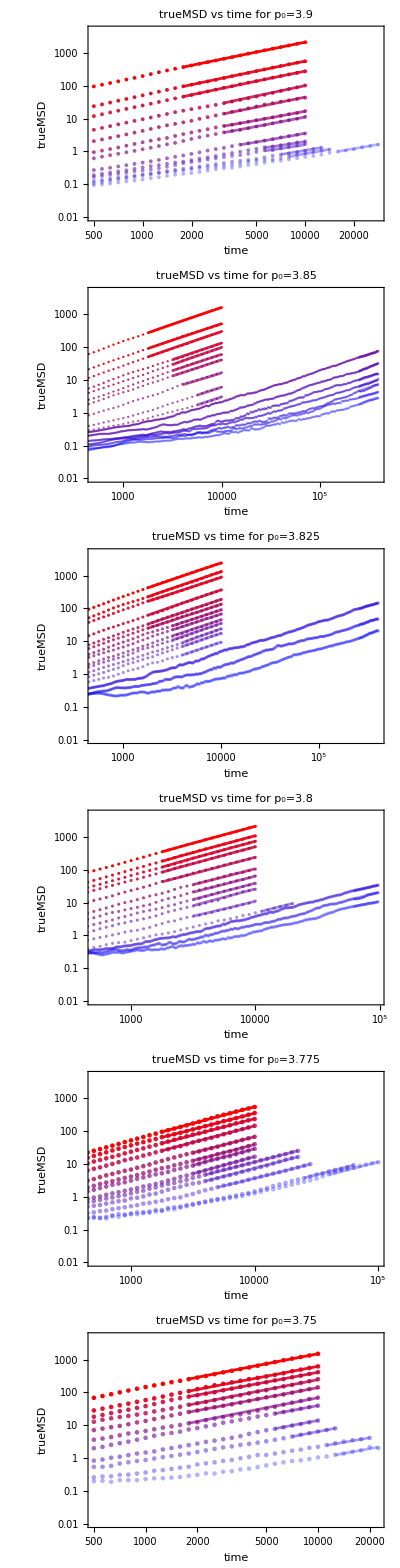

```mathematica
trueMSDMeanPlotsWithLinearFits=Table[Show[
ListLogLogPlot[Table[Table[{time[[p,T,rec+1]]-time[[p,T,1]],trueMSDMean[[p,T,rec]]},{rec,Length[CRTrueMSDMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","trueMSD"},ImageSize->600,PlotLabel->"trueMSD vs time for p_0="<>ToString[p0s[[p]]],Joined->False,PlotRange->{{500,All},{0.01,5000}},ImageSize->600],ListLogLogPlot[Table[Table[{time[[p,T,t+1]]-time[[p,T,1]],LinearFitsTrueMSD[[p,T]][time[[p,T,t+1]]-time[[p,T,Length[trueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]]]]+trueMSDMean[[p,T,Length[trueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]]-1]]},{t,Length[CRTrueMSDMean[[p,T]]]-fittingOffsetfromEnd[[p,T]],Length[CRTrueMSDMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],Joined->True]],{p,Length[p0s]}];
Column[trueMSDMeanPlotsWithLinearFits]
```

```mathematica
LinearFitsTrueMSD[[1,1]]["RSquared"]
```

0.999523

```mathematica
diffusionDeltatLinearFit=Table[Table[LinearFitsTrueMSD[[p,T]]["BestFitParameters"][[1]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{0.212073,0.0565147,0.0281499,0.0103112,0.00450248,0.0015783,0.00107541,0.000325992,0.000158728,0.000128986,0.0000907596,0.0000753184,0.0000514148},{0.162541,0.0517104,0.0300735,0.0133232,0.00997521,0.00599596,0.00405677,0.00154857,0.000594167,0.000295033,0.00018163,0.0000956523,0.0000408853,0.0000268118,0.000018372,0.000010204,7.78872×10^-6},{0.244834,0.132452,0.0877396,0.0370351,0.0188582,0.0132851,0.00899523,0.00663242,0.00449584,0.00355023,0.00250819,0.00176601,0.000932952,0.000332941,0.000126563,0.000064517},{0.211426,0.109407,0.0745306,0.050432,0.0238689,0.0104763,0.00627923,0.00385326,0.00262785,0.00102753,0.000451325,0.000301453,0.00019773,0.0000815716},{0.0551476,0.0346477,0.0237273,0.0143711,0.00658078,0.00386435,0.00285528,0.00168607,0.00111393,0.000726275,0.000338975,0.00014195,0.000113066},{0.150927,0.062172,0.0405191,0.0245749,0.0139122,0.0069132,0.00386682,0.00138189,0.000642508,0.000196519,0.0000927235}}

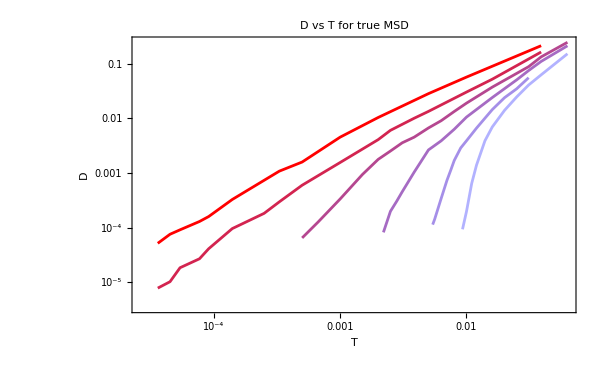

```mathematica
linearFitDiffusionConstPlots=ListLogLogPlot[Table[Table[{temperatures[[p,T]],LinearFitsTrueMSD[[p,T]]["BestFitParameters"][[1]]},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}],PlotStyle->redBluePlotConfig[Length[p0s]],FrameLabel->{"T","D"},PlotLabel->"D vs T for true MSD",Joined->True,ImageSize->600]
```

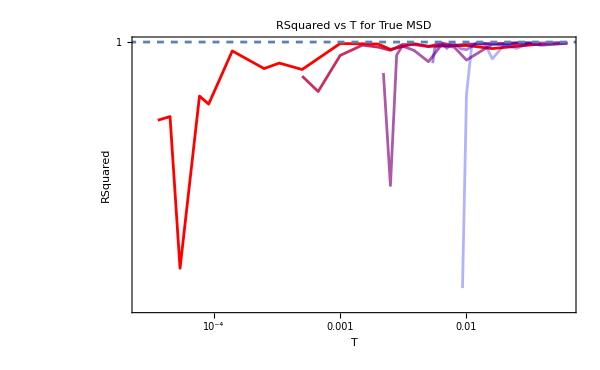

```mathematica
RSMSDPlots=Show[ListLogLogPlot[Table[Table[{temperatures[[p,T]],LinearFitsTrueMSD[[p,T]]["RSquared"]},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}],PlotStyle->redBluePlotConfig[Length[p0s]],FrameLabel->{"T","RSquared"},PlotLabel->"RSquared vs T for True MSD",Joined->True,ImageSize->600,PlotRange->All],LogLogPlot[1,{x,0.00001,1},PlotStyle->Dashed]]
```

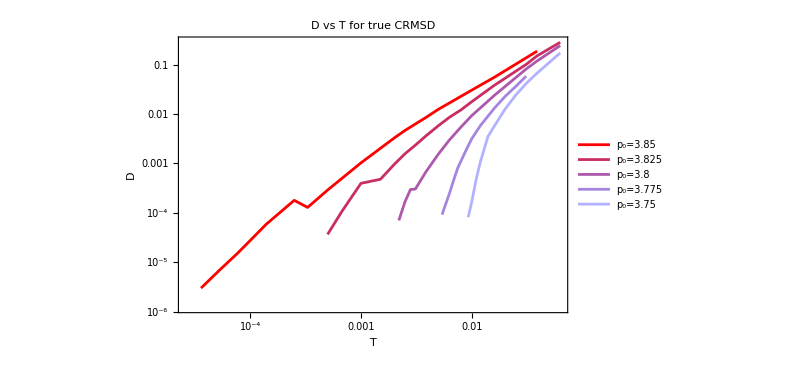

```mathematica
LinearFitCRdiffusionConstPlots=ListLogLogPlot[Table[Table[{temperatures[[p,T]],LinearFitsCRTrueMSD[[p,T]]["BestFitParameters"][[1]]},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}],PlotStyle->redBluePlotConfig[Length[p0s]],FrameLabel->{"T","D"},PlotLabel->"D vs T for true CRMSD",Joined->True,PlotLegends->Table["p_0="<>ToString[p0s[[p]]],{p,Length[p0s]}],ImageSize->600]
```

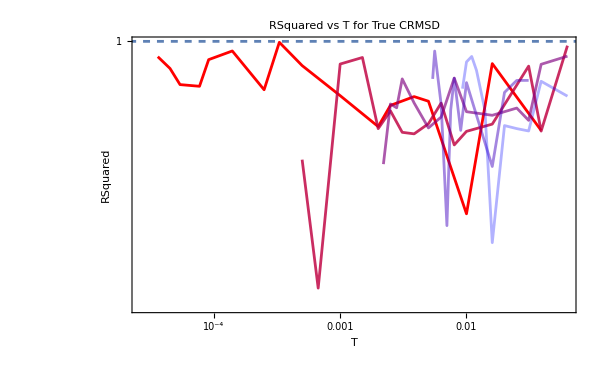

```mathematica
RSCRMSDPlots=Show[ListLogLogPlot[Table[Table[{temperatures[[p,T]],LinearFitsCRTrueMSD[[p,T]]["RSquared"]},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}],PlotStyle->redBluePlotConfig[Length[p0s]],FrameLabel->{"T","RSquared"},PlotLabel->"RSquared vs T for True CRMSD",Joined->True,ImageSize->600,PlotRange->All],LogLogPlot[1,{x,0.00001,1},PlotStyle->Dashed]]
```

```mathematica
Export["/home/chengling/Research/updates/05232024/MSDLinearfitting.jpeg",Grid[Partition[{linearFitDiffusionConstPlots,LinearFitCRdiffusionConstPlots,RSMSDPlots,RSCRMSDPlots},2]],ImageResolution->800]
```

/home/chengling/Research/updates/05232024/MSDLinearfitting.jpeg

```mathematica
Export["/home/chengling/Research/updates/05232024/MSDwithLinearfitting.jpeg",Grid[Partition[{trueMSDMeanPlotsWithLinearFits[[1]],CRTrueMSDMeanPlotsWithLinearFits[[1]],trueMSDMeanPlotsWithLinearFits[[2]],CRTrueMSDMeanPlotsWithLinearFits[[2]],trueMSDMeanPlotsWithLinearFits[[3]],CRTrueMSDMeanPlotsWithLinearFits[[3]]},2]],ImageResolution->800]
```

/home/chengling/Research/updates/05232024/MSDwithLinearfitting.jpeg

## export results

```mathematica
diffusion/4
```

{{0.0398288,0.0126947,0.00751401,0.00332879,0.00246796,0.00146995,0.00100918,0.000418351,0.000151209,0.0000769238,0.0000488036,0.0000203939,9.61958×10^-6,6.86562×10^-6,4.72194×10^-6,2.79334×10^-6,1.78801×10^-6},{0.0599479,0.0330051,0.0224001,0.00908335,0.00466978,0.00335485,0.0022786,0.00168387,0.00112863,0.000873372,0.00059,0.000430038,0.000231607,0.0000916225,0.0000297942,0.0000128192},{0.0520754,0.0266984,0.018285,0.0125015,0.00592636,0.00259435,0.00160845,0.000959747,0.000630688,0.000277502,0.000116194,0.0000861811,0.0000514096,0.0000268511},{0.0134848,0.00884055,0.00578186,0.00360842,0.00166818,0.000994575,0.000720343,0.000412399,0.000276731,0.000179884,0.0000870057,0.0000361786,0.0000280564},{0.0371741,0.0154551,0.0102795,0.00629496,0.00354814,0.00172563,0.000983439,0.000345812,0.000158686,0.0000512933,0.0000224688}}

```mathematica
diffusionDeltatLinearFit/4
```

{{0.0406352,0.0129276,0.00751837,0.00333079,0.0024938,0.00149899,0.00101419,0.000387144,0.000148542,0.0000737583,0.0000454074,0.0000239131,0.0000102213,6.70296×10^-6,4.59301×10^-6,2.551×10^-6,1.94718×10^-6},{0.0612084,0.0331131,0.0219349,0.00925878,0.00471454,0.00332127,0.00224881,0.00165811,0.00112396,0.000887556,0.000627047,0.000441502,0.000233238,0.0000832352,0.0000316407,0.0000161293},{0.0528565,0.0273517,0.0186326,0.012608,0.00596722,0.00261908,0.00156981,0.000963315,0.000656963,0.000256882,0.000112831,0.0000753631,0.0000494326,0.0000203929},{0.0137869,0.00866193,0.00593183,0.00359278,0.0016452,0.000966089,0.00071382,0.000421518,0.000278483,0.000181569,0.0000847438,0.0000354876,0.0000282665},{0.0377319,0.015543,0.0101298,0.00614372,0.00347805,0.0017283,0.000966704,0.000345471,0.000160627,0.0000491297,0.0000231809}}

```mathematica
diffusionDirectLinearFit/4
```

{{0.040572,0.01289,0.00750997,0.00328436,0.00250284,0.00150229,0.0010126,0.000406268,0.000150626,0.0000724054,0.0000448795,0.0000235286,0.0000102262,6.83759×10^-6,4.29198×10^-6,2.57012×10^-6,1.84916×10^-6},{0.0612654,0.0330435,0.0220193,0.00924768,0.00469833,0.00333201,0.00225908,0.00166865,0.00110662,0.0008675,0.00061817,0.000435723,0.000232222,0.0000857921,0.0000311404,0.0000156095},{0.0528906,0.0273985,0.0185863,0.0125955,0.00602476,0.00258915,0.00159649,0.00095607,0.000644946,0.000252293,0.000111332,0.0000729073,0.0000477676,0.0000192881},{0.0138568,0.00871115,0.00594594,0.00358291,0.00163838,0.000956432,0.000695817,0.000423893,0.000279067,0.000181125,0.0000851398,0.0000350008,0.000029119},{0.037659,0.0155503,0.010115,0.0061812,0.00349426,0.00172279,0.000968324,0.000335873,0.000161065,0.0000510402,0.0000235229}}

```mathematica
Δ
```

```mathematica
diffusionConstantTable=Table[Prepend[Table[{temperatures[[p,T]],diffusion[[p,T]]/4,diffusionDirectLinearFit[[p,T]]/4,diffusionDeltatLinearFit[[p,T]]/4},{T,Length[temperatures[[p]]]}],{"T","lim(t->inf)MSD/4t","fit MSD~4Dt for the tail","fit MSD~4Dt for the tail which is shifted to the origin"}],{p,Length[p0s]}]
```

{{{T,lim(t->inf)MSD/4t,fit MSD~4Dt for the tail,fit MSD~4Dt for the tail which is shifted to the origin},{0.039,0.0523105,0.052955,0.0530183},{0.01,0.0138385,0.0141622,0.0141287},{0.005,0.00685103,0.00702682,0.00703747},{0.002,0.00253778,0.00255751,0.00257781},{0.001,0.00107847,0.0011365,0.00112562},{0.0005,0.00042037,0.000396831,0.000394575},{0.00033,0.000282972,0.000271357,0.000268852},{0.00014,0.000087772,0.0000825948,0.000081498},{0.000091,0.0000501851,0.0000424749,0.0000396821},{0.000077,0.0000421058,0.0000351296,0.0000322465},{0.000054,0.0000256928,0.0000220067,0.0000226899},{0.000045,0.0000202385,0.0000189237,0.0000188296},{0.000036,0.0000143104,0.000012373,0.0000128537}},{{T,lim(t->inf)MSD/4t,fit MSD~4Dt for the tail,fit MSD~4Dt for the tail which is shifted to the origin},{0.039,0.0398288,0.040572,0.0406352},{0.016,0.0126947,0.01289,0.0129276},{0.01,0.00751401,0.00750997,0.00751837},{0.005,0.00332879,0.00328436,0.00333079},{0.00385,0.00246796,0.00250284,0.0024938},{0.0025,0.00146995,0.00150229,0.00149899},{0.002,0.00100918,0.0010126,0.00101419},{0.001,0.000418351,0.000406268,0.000387144},{0.0005,0.000151209,0.000150626,0.000148542},{0.00033,0.0000769238,0.0000724054,0.0000737583},{0.00025,0.0000488036,0.0000448795,0.0000454074},{0.00014,0.0000203939,0.0000235286,0.0000239131},{0.000091,9.61958×10^-6,0.0000102262,0.0000102213},{0.000077,6.86562×10^-6,6.83759×10^-6,6.70296×10^-6},{0.000054,4.72194×10^-6,4.29198×10^-6,4.59301×10^-6},{0.000045,2.79334×10^-6,2.57012×10^-6,2.551×10^-6},{0.000036,1.78801×10^-6,1.84916×10^-6,1.94718×10^-6}},{{T,lim(t->inf)MSD/4t,fit MSD~4Dt for the tail,fit MSD~4Dt for the tail which is shifted to the origin},{0.063,0.0599479,0.0612654,0.0612084},{0.039,0.0330051,0.0330435,0.0331131},{0.03105,0.0224001,0.0220193,0.0219349},{0.016,0.00908335,0.00924768,0.00925878},{0.01,0.00466978,0.00469833,0.00471454},{0.008,0.00335485,0.00333201,0.00332127},{0.0063,0.0022786,0.00225908,0.00224881},{0.005,0.00168387,0.00166865,0.00165811},{0.00385,0.00112863,0.00110662,0.00112396},{0.0031,0.000873372,0.0008675,0.000887556},{0.0025,0.00059,0.00061817,0.000627047},{0.002,0.000430038,0.000435723,0.000441502},{0.0015,0.000231607,0.000232222,0.000233238},{0.001,0.0000916225,0.0000857921,0.0000832352},{0.00067,0.0000297942,0.0000311404,0.0000316407},{0.0005,0.0000128192,0.0000156095,0.0000161293}},{{T,lim(t->inf)MSD/4t,fit MSD~4Dt for the tail,fit MSD~4Dt for the tail which is shifted to the origin},{0.063,0.0520754,0.0528906,0.0528565},{0.039,0.0266984,0.0273985,0.0273517},{0.03105,0.018285,0.0185863,0.0186326},{0.025,0.0125015,0.0125955,0.012608},{0.016,0.00592636,0.00602476,0.00596722},{0.01,0.00259435,0.00258915,0.00261908},{0.008,0.00160845,0.00159649,0.00156981},{0.0063,0.000959747,0.00095607,0.000963315},{0.005,0.000630688,0.000644946,0.000656963},{0.00385,0.000277502,0.000252293,0.000256882},{0.0031,0.000116194,0.000111332,0.000112831},{0.0028,0.0000861811,0.0000729073,0.0000753631},{0.0025,0.0000514096,0.0000477676,0.0000494326},{0.0022,0.0000268511,0.0000192881,0.0000203929}},{{T,lim(t->inf)MSD/4t,fit MSD~4Dt for the tail,fit MSD~4Dt for the tail which is shifted to the origin},{0.03105,0.0134848,0.0138568,0.0137869},{0.025,0.00884055,0.00871115,0.00866193},{0.02,0.00578186,0.00594594,0.00593183},{0.016,0.00360842,0.00358291,0.00359278},{0.012,0.00166818,0.00163838,0.0016452},{0.01,0.000994575,0.000956432,0.000966089},{0.009,0.000720343,0.000695817,0.00071382},{0.008,0.000412399,0.000423893,0.000421518},{0.0075,0.000276731,0.000279067,0.000278483},{0.007,0.000179884,0.000181125,0.000181569},{0.0063,0.0000870057,0.0000851398,0.0000847438},{0.0056,0.0000361786,0.0000350008,0.0000354876},{0.0054,0.0000280564,0.000029119,0.0000282665}},{{T,lim(t->inf)MSD/4t,fit MSD~4Dt for the tail,fit MSD~4Dt for the tail which is shifted to the origin},{0.063,0.0371741,0.037659,0.0377319},{0.039,0.0154551,0.0155503,0.015543},{0.03105,0.0102795,0.010115,0.0101298},{0.025,0.00629496,0.0061812,0.00614372},{0.02,0.00354814,0.00349426,0.00347805},{0.016,0.00172563,0.00172279,0.0017283},{0.014,0.000983439,0.000968324,0.000966704},{0.012,0.000345812,0.000335873,0.000345471},{0.011,0.000158686,0.000161065,0.000160627},{0.01,0.0000512933,0.0000510402,0.0000491297},{0.0093,0.0000224688,0.0000235229,0.0000231809}}}

```mathematica
Table[Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/diffudionConstantTableP"<>ToString[NumberForm[p0s[[p]],{5,3}]]<>".csv",diffusionConstantTable[[p]],"CSV"],{p,Length[p0s]}]
```

{/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/diffudionConstantTableP3.900.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/diffudionConstantTableP3.850.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/diffudionConstantTableP3.825.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/diffudionConstantTableP3.800.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/diffudionConstantTableP3.775.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/diffudionConstantTableP3.750.csv}

```mathematica
Export["/home/chengling/Research/updates/05312024/MSD.jpeg",Grid[Partition[trueMSDMeanPlots,2]],ImageResolution->800]
```

/home/chengling/Research/updates/05312024/MSD.jpeg

```mathematica
Export["/home/chengling/Research/updates/05312024/diffusionConstant.jpeg",diffusionConstPlots,ImageResolution->800]
```

/home/chengling/Research/updates/05312024/diffusionConstant.jpeg